```mathematica
SetDirectory["~/src/aoc/2023/06"]
```

/home/alex/src/aoc/2023/06

```mathematica
Fold[#1*#2&, Length/@MapThread[FindInstance[ToExpression[#1] b-b^2>ToExpression[#2],{b},Integers,200]&,Drop[#, 1]&/@StringSplit /@ StringSplit[ReadString["input"], "\n"]]]
```

449820

```mathematica
Length/@StringSplit /@ StringSplit[ReadString["input"], "\n"]
```

{5,5}

```mathematica
e=Apply[ToExpression[#1] b-b^2==ToExpression[#2]&,StringReplace[#," "->""]&/@First/@(Drop[#, 1]&/@(StringSplit[#, ":"]&/@ StringSplit[ReadString["input"], "\n"]))]
```

53717880 b-b^2==275118112151524

```mathematica
Solve[e,b]
```

{{b→2 (13429470-√111571136443019)},{b→2 (13429470+√111571136443019)}}

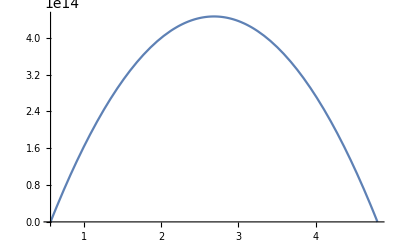

```mathematica
Plot[e,{b,2 (13429470+√111571136443019),2 (13429470-√111571136443019)}]
```

```mathematica
Floor[2 (13429470+√111571136443019)]-Ceiling[2 (13429470-√111571136443019)]+1
```

42250895